## Section | Exoplanets

Ordinarily, pulsars are highly regular astronomical clocks. Suppose however that the pulsar has one heavy unseen companion. Then the pulsar will orbit around the centre of mass of the combined system, sometimes moving towards the earth and sometimes away from it.  This will lead to a sinusoidal variation in the timings as measured by an earth-based observer. If there is more than one unseen companion the timing variation will be more complicated but, to a good approximation, will be a linear superposition of sinusoidal variations with differing periods.

Wolszczan and Frail (1992) and Wolszczan (1994) studied timing variations for the pulsar PSR B1257+12 over a 3-year period. The timing variations for PSR B1257+12 indicate that it is orbited by at least two "planets".  The data in  (kindly supplied by Alex Wolszczan) represents post-fit residuals after fitting out a standard timing model assuming a single pulsar (i.e., taking into account the earth's orbital motion, etc).

In this chapter we fit a double planet model to the  and determine the orbital periods of each planet.

### Dataset

Convert the data file to a structured Dataset based on a hierarchy of lists and associations:

```mathematica
headers={"n","epoch","residual","phase","error"};
```

```mathematica
dataset=Dataset@(AssociationThread[headers->##]&/@)
```

Use Keys to ListPlot the residual versus epoch:

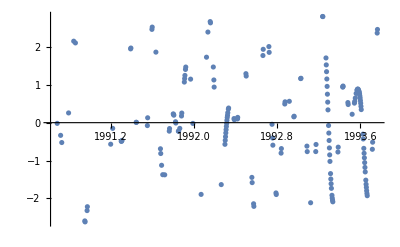

```mathematica
dataset[ListPlot,{"epoch","residual"}]
```

### EventSeries

One can also turn the structured Dataset into an EventSeries:

```mathematica
events=EventSeries@Normal@dataset[All,{"epoch",{"residual","phase"}}]
```

EventSeries[…]

### Time Series

Create a TimeSeries from the residual (in ms), versus the epoch, (time in decimal years, minus 1990):

```mathematica
ts=TimeSeries[Normal@dataset⟦All,"residual"⟧,{Normal@dataset⟦All,"epoch"⟧-1990}]
```

TimeSeries[…]

This TimeSeries permits directly extraction of the following information:

```mathematica
ts["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathComponent,PathComponents,PathFunction,PathLength,Times,ValueDimensions,Values}

Extract the minimum time value, in decimal years:

```mathematica
ts["FirstTime"]
```

0.687021

### Residuals

Visualize the residuals:

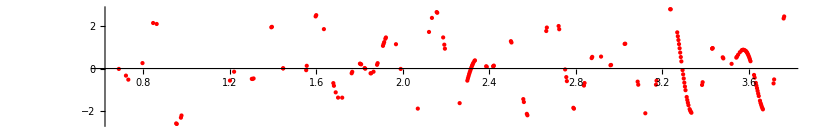

```mathematica
residuals=ListPlot[ts,AspectRatio->1/6,PlotStyle->{Red,AbsolutePointSize[3]}]
```

The data is not evenly spaced. However, in regions where there is sufficient data, it does look like it might be explained by a linear superposition of sinusoidal variations of differing periods.

### Discrete Fourier transform

The discrete Fourier transform (DFT) can be used to determine the principal frequencies of a periodic system. However, Fourier can only be used for uniformly sampled data. One way to approximately determine the orbital frequencies is to interpolate the timing data, re-sample it uniformly, and then apply Fourier. This is somewhat clumsy and introduces additional numerical error.

### Periodogram

There is a simple spectral analysis method that avoids interpolation and resampling: For each frequency ω, fit α and β in α sin(ω t)+β cos(ω t) to the data by linear least-squares (i.e., using Fit). The spectral energy ℰ(ω) is then the square amplitude integrated over one period, T=2 π/ω (normalised by dividing by T). This is, essentially, the Lomb-Scargle Periodogram as discussed in Press et al. (2011).

### Spectral Energy

To determine good starting values for nonlinear fitting, one approach is to extract these from the maxima of the spectral density.

Since

(∫_0^((2 π)/ω) (α sin(ω t)+β cos(ω t))^2 ⅆt)/(∫_0^((2 π)/ω) 1ⅆt)==1/2 (α^2+β^2)

the spectral energy or spectral density ℰ(ω) of (α sin(ω t)+β cos(ω t)) is ℰ(ω)=1/2 (α^2+β^2) .

Use  pattern-matching to compute the spectral density for the time series:

```mathematica
ℰ[ω_?NumericQ]:=Fit[Normal[ts],{Sin[ω t],Cos[ω t]},t]/.α_ Sin[t_]+β_ Cos[t_]:>1/2 (α^2+β^2)
```

The use of the replacement rule α_ sin(t_)+β_ cos(t_):>1/2 (α^2+β^2), is somewhat subtle. It effectively uses pattern-matching to compute the normalized integral over one period. we can use pattern-matching to replace specific expressions of the form α_ sin(t_)+β_ cos(t_) with its normalised square-integral over one period, 1/2 (α^2+β^2). This is fast and does not involve using (numerical) integration.

Plot ℰ(ω) as a function of ω:

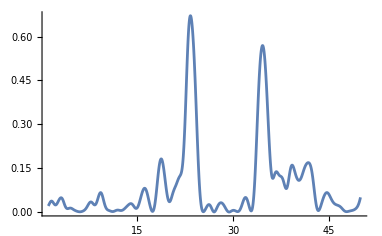

```mathematica
Plot[ℰ[ω],{ω,1,50},PlotRange->All]
```

This graph reveals peaks at a number of frequencies.

### Principal Frequencies

Determine the two principal frequencies for 20<=ω<=40 finding those peaks with values greater than 0.5:

```mathematica
tsmax=TimeSeries@Table[{ω,ℰ[ω]},{ω,20,40,0.01}]
```

TimeSeries[…]

```mathematica
peaks=FindPeaks[tsmax,Automatic,Automatic,0.5]
```

TimeSeries[…]

Highlight the two principal frequencies:

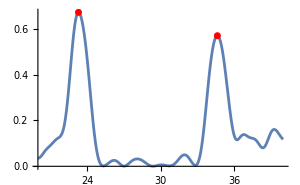

```mathematica
Plot[ℰ[ω],{ω,20,40},PlotRange->All,Epilog->{Red,AbsolutePointSize[5],Point@Normal@peaks}]
```

Extract the values of the  principal frequencies for further analysis:

```mathematica
{Subscript[ω, 1],Subscript[ω, 2]}=peaks["Times"]
```

{23.31,34.64}

### Periods

These two frequencies correspond to “planets” orbiting the pulsar with approximate orbital period determined by 𝒯==2π/ω:

Compute the approximate orbital periods 𝒯_1 and 𝒯_2:

```mathematica
Subscript[𝒯, 1]=(2π)/Subscript[ω, 1] 365.24 Quantity[, "Days"]
```

98.45 days

```mathematica
Subscript[𝒯, 2]=(2π)/Subscript[ω, 2] 365.24 Quantity[, "Days"]
```

66.2492 days

### Nonlinear Fit

Since we now have good estimates for the orbital periods, it is easy to do a nonlinear fit of a double planet model of the form a sin(γ+θ t)+b sin(δ+t ϕ)+ϵ.

Use NonlinearModelFit to find the principal frequencies determined in the previous section to determine the optimal values of a,  b,  θ,  γ,  ϕ,  δ,  and ϵ. The principal frequencies provide good starting values for θ and ϕ in the nonlinear fitting routine:

```mathematica
nlmf=NonlinearModelFit[ts,a Sin[θ t+γ]+b Sin[ϕ t+δ]+ϵ,{{a,1},{b,1},{θ,Subscript[ω, 1]},{ϕ,Subscript[ω, 2]},{γ,0},{δ,0},{ϵ,0}},t]
```

FittedModel[…]

Extract the best fit parameters:

```mathematica
nlmf["BestFitParameters"]
```

{a→1.41015,b→-1.31483,θ→23.3869,ϕ→34.5111,γ→1.23765,δ→-0.160043,ϵ→0.0769581}

We use estimated values of a≈1 and b≈1 from the plot of the residuals above and set the remaining parameters to 0.

Note the slight shift in the values of the two principal frequencies:

```mathematica
{Abs[Subscript[ω, 1]-θ],Abs[Subscript[ω, 2]-ϕ]}/.%
```

{0.0769384,0.128905}

Compare the resulting best-fit with the timing residuals:

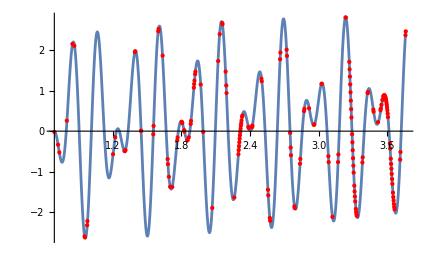

```mathematica
Plot[nlmf[t],{t,ts["FirstTime"],ts["LastTime"]},Epilog->residuals⟦1⟧]
```

This plot shows the quality of the nonlinear fit.

References

Wolszczan, A. & Frail, D., 1992, Nature, 255:145, “A Planetary System around the Millisecond Pulsar PSR1257+12”;

Wolszczan, A., 1994, Science, 264:538, “Confirmation of Earth-Mass Planets Orbiting the Millisecond Pulsar PSR B1257+12”.

Spectral Analysis of Unevenly Sampled Data in Numerical Recipes: The Art of Scientific Computing, Third Edition, by W.H. Press, S.A. Teukolsky, W.T. Vetterling, and B.P. Flannery. Version 3.04 (2011).